```mathematica
F[x_, a_] := Tan[x]+ a * x
```

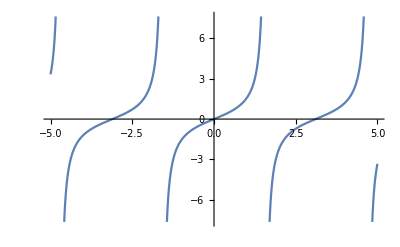

```mathematica
Plot[F[x, 0.0107], {x, -5, 5}]
```

```mathematica
FindRoot[F[x, 0.0107] == 0, {x, π}]
```

{x→3.10835}

```mathematica
FindRoot[F[x, 0.0107] == 0, {x, -π}]
```

{x→-3.10835}

```mathematica
FindRoot[F[x,0.0107] == 0, {x, -2π}]
```

```mathematica
{x->-6.216763787235575}
```